```mathematica
S={{1,-1}};
Ex={{-k1},{k2}};
Ep={{C1-X,0},{0,X-C2}};
Cs=-Inverse[S.Ex].S;
CJ=Simplify[IdentityMatrix[2]+Ex.Cs];
RJ=Simplify[CJ.Ep/.X->(k1*C1+k2*C2)/(k1+k2)]/.{C1->2,C2->1,k1->1,k2->2}
```

{{4/9,1/9},{4/9,1/9}}

```mathematica
N[4/9]
```

0.444444

```mathematica
CJ
```

{{k2/(k1+k2),k1/(k1+k2)},{k2/(k1+k2),k1/(k1+k2)}}

```mathematica
S={{1,-1}};
Ex={{-k1},{2*k2}};
Ep={{C1-X,0},{0,2*(X-C2)}};
Cs=-Inverse[S.Ex].S;
CJ=Simplify[IdentityMatrix[2]+Ex.Cs];
RJ=N[Simplify[CJ.Ep/.X->(k1*C1+2*k2*C2)/(k1+2*k2)]/.{C1->2,C2->1,k1->1,k2->2}]
```

{{0.64,0.08},{0.64,0.08}}

```mathematica
sol=FullSimplify[DSolve[{x1'[t]==-k(x1[t]-x2[t]),x2'[t]==k(x1[t]-x2[t])-x2[t],x1[0]==1,x2[0]==0},{x1,x2},t]]
```

{{x1→Function[{t},1/(2 √(1+4 k^2))(-ⅇ^(1/2 (-1-2 k-√(1+4 k^2)) t)+ⅇ^(1/2 (-1-2 k+√(1+4 k^2)) t)+ⅇ^(1/2 (-1-2 k-√(1+4 k^2)) t) √(1+4 k^2)+ⅇ^(1/2 (-1-2 k+√(1+4 k^2)) t) √(1+4 k^2))],x2→Function[{t},-((ⅇ^(1/2 (-1-2 k-√(1+4 k^2)) t)-ⅇ^(1/2 (-1-2 k+√(1+4 k^2)) t)) k)/(√(1+4 k^2))]}}

```mathematica
A={{-k,k},{k,-(k+1)}};
A//MatrixForm
```

(-k | k
k | -1-k)

```mathematica
TeXForm[Eigenvalues[A]]
Eigenvalues[A]
Eigenvectors[A]
```

{1/2 (-1-2 k-√(1+4 k^2)),1/2 (-1-2 k+√(1+4 k^2))}

{{-(-1+√(1+4 k^2))/(2 k),1},{-(-1-√(1+4 k^2))/(2 k),1}}

\left\{\frac{1}{2} \left(-\sqrt{4 k^2+1}-2 k-1\right),\frac{1}{2} \left(\sqrt{4 k^2+1}-2
   k-1\right)\right\}

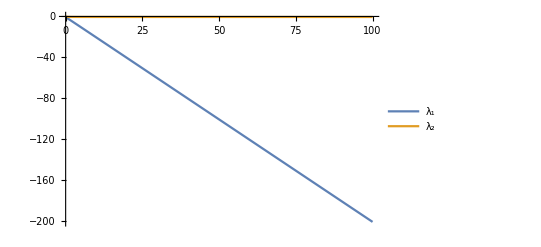

```mathematica
Plot[{λ1,λ2},{k,0,100},PlotLegends->{"λ_1","λ_2"}]
```

```mathematica
Simplify[D[(Vf*c/(1+c)x-Vb*p/(1+c))/(1+x+p/(1+c)),c]]
```

(Vf x (1+x)+p (Vb+Vb x+Vf x))/(1+c+p+x+c x)^2

```mathematica
S={{-1,1,0,0},{2,-1,-1,0},{0,-1,0,1},{0,1,0,-1}};
Sr={{-1,1,0,0},{2,-1,-1,0},{0,-1,0,1}};
L={{1,0,0},{0,1,0},{0,0,1},{0,0,-1}};
Es={{e11,e12,0,0},{e21,e22,e23,e24},{0,e32,0,0},{0,0,e43,e44}};
M=Sr.Es.L;
MatrixForm[S]
MatrixForm[Es]
L.Sr==S
```

(-1 | 1 | 0 | 0
2 | -1 | -1 | 0
0 | -1 | 0 | 1
0 | 1 | 0 | -1)

(e11 | e12 | 0 | 0
e21 | e22 | e23 | e24
0 | e32 | 0 | 0
0 | 0 | e43 | e44)

True

```mathematica
Cs=Simplify[-L.Inverse[M].Sr];
Cs[[3,1]]
```

(e21 e32)/(e11 (e23 e32-e24 e32+(e22-e32) (e43-e44))-e21 (e12-e32) (e43-e44))

```mathematica
MatrixForm[Es]
MatrixForm[{{"+","-",0,0},{"-","+","+","-"},{0,"+",0,0},{0,0,"-","+"}}]
```

(e11 | e12 | 0 | 0
e21 | e22 | e23 | e24
0 | e32 | 0 | 0
0 | 0 | e43 | e44)

(+ | - | 0 | 0
- | + | + | -
0 | + | 0 | 0
0 | 0 | - | +)

```mathematica
-    +   ;
(e21 e32)/(e11 (e23 e32-e24 e32+(e22-e32) (e43-e44))-e21 (e12-e32) (e43-e44));
   +       +     +        -     +            +       +         -        +             -        -         +          -       +
```

```mathematica
Factor[e11 (e23 e32-e24 e32+(e22-e32) (e43-e44))-e21 (e12-e32) (e43-e44)]
```

```mathematica
+     +     +        +     -     +         -     -    -           +     +     -        +    -     -           -     +     -        -     -     +           +     +     +          +     +    +         -     +     +               ;
e11 e23 e32-e11 e24 e32-e12 e21 e43+(e11 e22 e43-e11 e32 e43)+e21 e32 e43+e12 e21 e44-(e11 e22 e44)+e11 e32 e44-e21 e32 e44;
```

```mathematica
e11 (e23 e32-e24 e32)+(e11(e22-e32)-e21 (e12-e32) ) (e43-e44);
   +       +     +        -     +            +      +        +     +        -     -        -     +          -        +                       ;
e11 (e23 e32-e24 e32)+(e11 e22-e11 e32-e21 e12+e21 e32)(e43-e44);
   +    +       +         -              +        -          +     +        -     -        -     +         +     +                    ;
e11 e32(e23 -e24 )+(e44-e43)(e11 e32+e21 e12-e21 e32-e11 e22);
```

```mathematica
Simplify[Solve[{k1(C1*X1-X2^2)==k2(X2-X1),k2(X2-X1)==k3(X2-C2)},{X1,X2}]]
```

{{X1→(C1 k1 (k2-k3)^2+2 C2 k1 k2 k3+(k2-k3) (-k2 k3+√(C1^2 k1^2 (k2-k3)^2+k2^2 k3 (4 C2 k1+k3)+2 C1 k1 k2 k3 (2 C2 k1-k2+k3))))/(2 k1 k2^2),X2→(C1 k1 k2-C1 k1 k3-k2 k3+√(4 C2 k1 k2 (C1 k1+k2) k3+(C1 k1 (k2-k3)-k2 k3)^2))/(2 k1 k2)},{X1→(C1 k1 (k2-k3)^2+2 C2 k1 k2 k3-(k2-k3) (k2 k3+√(C1^2 k1^2 (k2-k3)^2+k2^2 k3 (4 C2 k1+k3)+2 C1 k1 k2 k3 (2 C2 k1-k2+k3))))/(2 k1 k2^2),X2→-(-C1 k1 k2+C1 k1 k3+k2 k3+√(4 C2 k1 k2 (C1 k1+k2) k3+(C1 k1 (k2-k3)-k2 k3)^2))/(2 k1 k2)}}

```mathematica
J=Simplify[k3(X2-C2)/.X2->(C1 k1 k2-C1 k1 k3-k2 k3+√(4 C2 k1 k2 (C1 k1+k2) k3+(C1 k1 (k2-k3)-k2 k3)^2))/(2 k1 k2)]
```

k3 (-C2+(C1 k1 k2-C1 k1 k3-k2 k3+√(4 C2 k1 k2 (C1 k1+k2) k3+(C1 k1 (k2-k3)-k2 k3)^2))/(2 k1 k2))

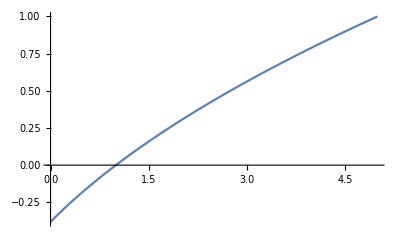

```mathematica
Plot[J/.{k1->1,k2->1,k3->1,C2->1},{C1,0,5}]
```

```mathematica
Solve[k1(C1-X/K1)==k2(X-C2/K2),X]
```

{{X→(K1 (C2 k2+C1 k1 K2))/((k1+K1 k2) K2)}}

```mathematica
Simplify[k1(C1-X/K1)/.X->(K1 (C2 k2+C1 k1 K2))/((k1+K1 k2) K2)]
```

(k1 (-C2 k2+C1 K1 k2 K2))/((k1+K1 k2) K2)

```mathematica
Solve[k1f C1-k1b X==k2f X-k2b C2,X]
```

{{X→(C1 k1f+C2 k2b)/(k1b+k2f)}}

```mathematica
Simplify[k1f C1-k1b X/.X->(C1 k1f+C2 k2b)/(k1b+k2f)]
```

(-C2 k1b k2b+C1 k1f k2f)/(k1b+k2f)

```mathematica
Limit[(Vf X/KX-Vb Y/KY)/(1+X/KX+Y/KY),KY->Infinity]
```

(Vf X)/(KX+X)

```mathematica
n1=V1f (r*C1)/K1C1-V1b X/K1X;
d1=1+ (r*C1)/K1C1+ X/K1X;
n2=V2f X/K2X-V2b C2/K2C2;
d2=1+ X/K2X+ C2/K2C2;
```

```mathematica
Collect[(d2*n1-d1*n2)/.{C1->2,C2->1},X,Simplify]
```

(K1C1 V2b+2 r (V1f+K2C2 V1f+V2b))/(K1C1 K2C2)+((2 K1X K2C2 r (V1f-V2f)-K1C1 (K2X (V1b+K2C2 V1b-V2b)+K1X K2C2 V2f)) X)/(K1C1 K1X K2C2 K2X)-((V1b+V2f) X^2)/(K1X K2X)

```mathematica
(p1*r+p2)+(p3*r+p4)X+p5 X^2
(p1/p5*r+p2/p5)+(p3/p5*r+p4/p5)X+ X^2=
(θ1*r+θ2)+(θ3*r+θ4)X+X^2
```

```mathematica
p1 =Simplify[(2 (V1f+K2C2 V1f+V2b))/(K1C1 K2C2)]
p2 =Simplify[ (K1C1 V2b)/(K1C1 K2C2)]
p3=Simplify[(2 K1X K2C2 (V1f-V2f))/(K1C1 K1X K2C2 K2X)]
p4=Simplify[(-K1C1 (K2X (V1b+K2C2 V1b-V2b)+K1X K2C2 V2f))/(K1C1 K1X K2C2 K2X)]
p5=Simplify[-(V1b+V2f)/(K1X K2X)]
```

(2 (V1f+K2C2 V1f+V2b))/(K1C1 K2C2)

V2b/K2C2

(2 (V1f-V2f))/(K1C1 K2X)

-(K2X (V1b+K2C2 V1b-V2b)+K1X K2C2 V2f)/(K1X K2C2 K2X)

-(V1b+V2f)/(K1X K2X)

```mathematica
h[V1f_,V1b_,K1C1_,K1X_,V2f_,V2b_,K2X_,K2C2_]={p1/p5,p2/p5,p3/p5,p4/p5};
```

```mathematica
Jacbn[V1f_,V1b_,K1C1_,K1X_,V2f_,V2b_,K2X_,K2C2_]=D[h[V1f,V1b,K1C1,K1X,V2f,V2b,K2X,K2C2],{{V1f,V1b,K1C1,K1X,V2f,V2b,K2X,K2C2}}];
```

```mathematica
JacMat=Jacbn[1,1,1,1,1,1,1,1]
```

{{-2,3/2,3,-3,3/2,-1,-3,2},{0,1/4,0,-1/2,1/4,-1/2,-1/2,1/2},{-1,0,0,0,1,0,0,0},{0,1/2,0,1/2,0,-1/2,1/2,0}}

```mathematica
V=N[SingularValueDecomposition[JacMat][[3]]]
```

{{0.319759,-0.645413,0.0876111,-0.200469,0.,0.,0.,0.658281},{-0.231234,-0.0336631,0.592896,0.164939,-0.471405,-0.166667,0.560449,0.050637},{-0.459146,-0.136397,0.0597265,0.730534,0.235702,0.0833333,-0.280224,0.303822},{0.472462,0.255952,0.303855,0.228634,0.471405,-0.583333,0.040032,0.050637},{-0.248227,0.639806,-0.0310817,-0.307786,0.,0.,0.,0.658281},{0.159702,0.0392699,-0.649426,0.343316,0.,0.,0.640513,0.151911},{0.472462,0.255952,0.303855,0.228634,0.,0.75,0.040032,0.050637},{-0.316082,-0.147611,0.172785,-0.285975,0.707107,0.25,0.440352,-0.101274}}

```mathematica
V[[All,-5]]
```

{-0.200469,0.164939,0.730534,0.228634,-0.307786,0.343316,0.228634,-0.285975}

```mathematica
JacMat.V[[All,-5]]
```

{0.0911976,-0.578992,-0.107318,0.139446}

```mathematica
ClearAll["Global`*"]
```

```mathematica
a=10;
f[p1_,p2_,ϵ_]:={Sin[p1]+Cos[p2+ϵ],Sin[p1]+Cos[p2+2ϵ],Sin[p1]+Cos[p2+3ϵ]}*5;
fλ[p1_,p2_,λ_,ϵ_]:=λ*f[p1,p2,ϵ]+(1-λ)*{p1,p2,0};
Manipulate[Show[{ParametricPlot3D[fλ[p1,p2,λ,ϵ],{p1,-10,10},{p2,-10,10} ,AxesLabel->{"y1","y2","y3"},PlotRange->{{-a,a},{-a,a},{-a,a}},PlotStyle->Opacity[0.01],Mesh->2],ListPointPlot3D[Table[fλ[i,i,λ,ϵ],{i,-10,10,0.1}],PlotStyle->Red],ListPointPlot3D[Table[fλ[i,-10,λ,ϵ],{i,-10,10,0.1}],PlotStyle->Blue],ListPointPlot3D[Table[fλ[-10,i,λ,ϵ],{i,-10,10,0.1}],PlotStyle->Green],ListPointPlot3D[Table[fλ[i,10,λ,ϵ],{i,-10,10,0.1}],PlotStyle->Cyan],ListPointPlot3D[Table[fλ[10,i,λ,ϵ],{i,-10,10,0.1}],PlotStyle->Magenta]}],{λ,{0.99,1}},{ϵ,{0,0.01,0.1,0.2,0.3,0.4,0.5,1}}]
```

ParametricPlot3D::prng: Value of option PlotRange -> {{-a, a}, {-a, a}, {-a, a}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPointPlot3D::arrayerr: {fλ[-10., -10., 1., 0.], fλ[-9.9, -10., 1., 0.], fλ[-9.8, -10., 1., 0.], fλ[-9.7, -10., 1., 0.], fλ[-9.6, -10., 1., 0.], fλ[-9.5, -10., 1., 0.], fλ[-9.4, -10., 1., 0.], fλ[-9.3, -10., 1., 0.], fλ[-9.2, -10., 1., 0.], fλ[-9.1, -10., 1., 0.], « 31 », fλ[-5.9, -10., 1., 0.], fλ[-5.8, -10., 1., 0.], fλ[-5.7, -10., 1., 0.], fλ[-5.6, -10., 1., 0.], fλ[-5.5, -10., 1., 0.], fλ[-5.4, -10., 1., 0.], fλ[-5.3, -10., 1., 0.], fλ[-5.2, -10., 1., 0.], fλ[-5.1, -10., 1., 0.], « 151 »} must be a valid array or a list of valid arrays.

```mathematica
ClearAll["Global`*"]
```

```mathematica
a=6;b=3; ϵ=1;
f[logp1_,logp2_,ϵ_]:={logp1+Log[Exp[logp2]+ϵ],logp1+Log[Exp[logp2]+2ϵ],logp1+Log[Exp[logp2]+3ϵ]};
fλ[logp1_,logp2_,λ_,ϵ_]:=λ*f[logp1,logp2,ϵ]+(1-λ)*{logp1,logp2,0}*2;
Manipulate[Show[{ParametricPlot3D[fλ[logp1,logp2,λ,ϵ],{logp1,-b,b},{logp2,-b,b} ,AxesLabel->{"y1","y2","y3"},PlotRange->{{-a,a},{-a,a},{-a,a}},PlotStyle->Opacity[0.1],Mesh->2],
ListPointPlot3D[Table[fλ[i,i,λ,ϵ],{i,-b,b,0.1}],PlotStyle->Red],ListPointPlot3D[Table[fλ[i,-b,λ,ϵ],{i,-b,b,0.1}],PlotStyle->Blue],ListPointPlot3D[Table[fλ[-b,i,λ,ϵ],{i,-b,b,0.1}],PlotStyle->Green],ListPointPlot3D[Table[fλ[i,b,λ,ϵ],{i,-b,b,0.1}],PlotStyle->Cyan],ListPointPlot3D[Table[fλ[b,i,λ,ϵ],{i,-b,b,0.1}],PlotStyle->Magenta]}],{λ,0,1},{ϵ,0,6}]
```

```mathematica
Collect[(k1f*r*C1-k1b*X)-(k2f*X-k2b*C2)/.{C1->2,C2->1},X,Simplify]
```

k2b+2 k1f r+(-k1b-k2f) X

```mathematica
n1=V1f X1/K1X1 C1/K1C1-V1b X2^2/K1X2^2;
d1=1+X1/K1X1+C1/K1C1+X1/K1X1 C1/K1C1+(2 X2)/K1X2+X2^2/K1X2^2;
n2=V2f X2/K2X2 X3/K2X3-V2b
```